The Langevin function is

```mathematica
L[x_]:=Coth[x]-1/x
```

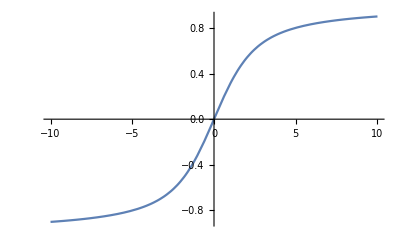

```mathematica
Plot[
L[x],{x,-10,10}
]
```

Giving M in units of M_s and parameter a in units of μ_0, we can solve the Weiss mean field equation:

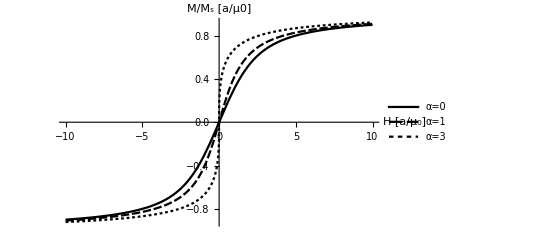

```mathematica
a=1;
plot=Plot[
{
L[H/a],
M/.FindRoot[(L[(H+α M)/a]/.{α->1})-M,{M,1}],
M/.FindRoot[(L[(H+α M)/a]/.{α->3})-M,{M,1}]
},
{H,-10,10},
PlotLegends->Placed[{"α=0","α=1","α=3"},Top],
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
]
```

```mathematica
Export["C:\\Users\\Jakob\\Documents\\CENTREX Jakob\\0 common\\thesis\\figs\\mathematica\\weiss.pdf",plot]
```

C:\Users\Jakob\Documents\CENTREX Jakob\0 common\thesis\figs\mathematica\weiss.pdf

#### Jiles-Atherton

The Langevin function is

```mathematica
L[x_]:=Coth[x]-1/x
```

A hysteresis loop is found by numerically integrating the Jiles-Atherton differential equation for the forward and backward motion:

```mathematica
loop[k_,a_,α_,Hi_,Hf_,Mi_,Mf_]:={
M[H]/.NDSolve[
{k M'[H]==L[(H+α M[H])/a]-M[H],M[Hi]==Mi},
M,{H,Hi,Hf}],
M[H]/.NDSolve[
{-k M'[H]==L[(H+α M[H])/a]-M[H],M[Hf]==Mf},
M,{H,Hf,Hi}]
}
```

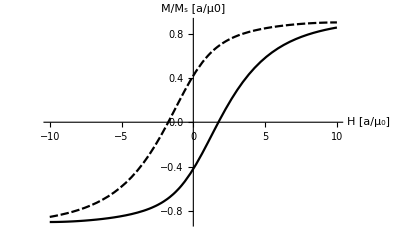

```mathematica
Plot[
Evaluate[loop[2,1,0.0033,-10,10,-.9,.9]],
{H,-10,10},
PlotRange->{{-10,10},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
]
```

#### Spiral

```mathematica
Hi=-10;
Hf=10;
Mi=-.85;
a=1;
α=0.0033;
k=2;
decay=0.5;
```

Initial loop:

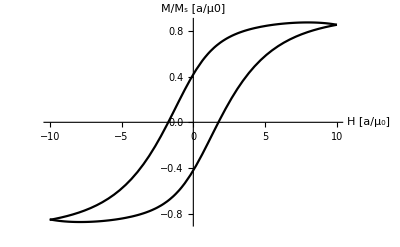

```mathematica
Mforward[H_]=M[H]/.NDSolve[
{k M'[H]==L[(H+α M[H])/a]-M[H],M[Hi]==Mi},
M,{H,Hi,Hf}];
pf0=Plot[
Evaluate[Mforward[H]],
{H,Hi,Hf},
PlotRange->{{Hi,Hf},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
];
Mbackward[H_]=M[H]/.NDSolve[
{-k M'[H]==L[(H+α M[H])/a]-M[H],M[Hf]==Mforward[Hf]},
M,{H,Hf,Hi}];
pb0=Plot[
Evaluate[Mbackward[H]],
{H,Hi,Hf},
PlotRange->{{Hi,Hf},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
];
Show[pf0,pb0]
```

Subsequent loops

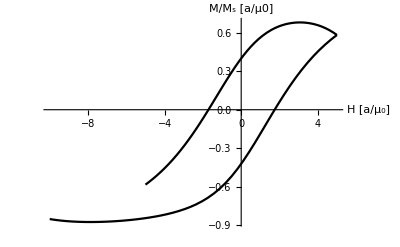

```mathematica
Hf = Hf * decay;
Mforward[H_]=M[H]/.NDSolve[
{k M'[H]==L[(H+α M[H])/a]-M[H],M[Hi]==Mi},
M,{H,Hi,Hf}];
pf1=Plot[
Evaluate[Mforward[H]],
{H,Hi,Hf},
PlotRange->{{Hi,Hf},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
];
Hi=Hi*decay;
Mbackward[H_]=M[H]/.NDSolve[
{-k M'[H]==L[(H+α M[H])/a]-M[H],M[Hf]==Mforward[Hf]},
M,{H,Hf,Hi}];
pb1=Plot[
Evaluate[Mbackward[H]],
{H,Hi,Hf},
PlotRange->{{Hi,Hf},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
];
Show[pf1,pb1]
```

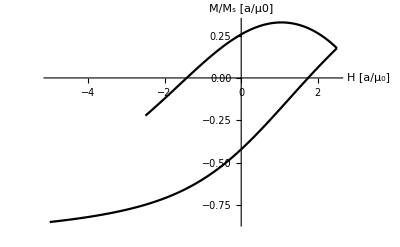

```mathematica
Hf = Hf * decay;
Mforward[H_]=M[H]/.NDSolve[
{k M'[H]==L[(H+α M[H])/a]-M[H],M[Hi]==Mi},
M,{H,Hi,Hf}];
pf2=Plot[
Evaluate[Mforward[H]],
{H,Hi,Hf},
PlotRange->{{Hi,Hf},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
];
Hi=Hi*decay;
Mbackward[H_]=M[H]/.NDSolve[
{-k M'[H]==L[(H+α M[H])/a]-M[H],M[Hf]==Mforward[Hf]},
M,{H,Hf,Hi}];
pb2=Plot[
Evaluate[Mbackward[H]],
{H,Hi,Hf},
PlotRange->{{Hi,Hf},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
];
Show[pf2,pb2]
```

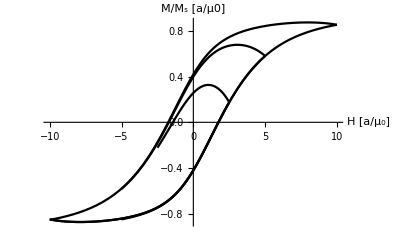

```mathematica
Show[pf0,pb0,pf1,pb1,pf2,pb2]
```

#### Spiral 2

```mathematica
L[x_]:=Coth[x]-1/x
```

```mathematica
Hi0=-10;
Hf0=10;
Mi0=-.85;
a=1;
α=0.0033;
k=2;
decay=0.5;
Ntotal=3;
```

```mathematica
M0=M/.NDSolve[{k M'[H]==L[(H+α M[H])/a]-M[H],M[Hi]==Mi0},M,{H,Hi,Hf}]⟦1,1⟧;
```

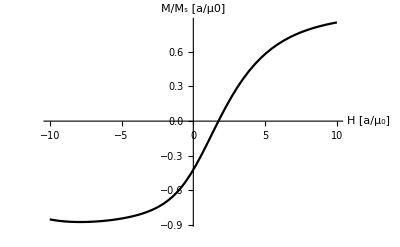

```mathematica
Plot[
Evaluate[M0[H]],
{H,Hi,Hf},
PlotRange->{{Hi,Hf},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
]
```

```mathematica
Mnext[Mprev_,δ_]:=M/.NDSolve[
{(-1)^(δ+1) k M'[H]==L[(H+α M[H])/a]-M[H],M[Mprev["Domain"]⟦1,δ⟧]==Mprev[Mprev["Domain"]⟦1,δ⟧]},
M,{H,Mprev["Domain"]⟦1,Mod[δ+1,2]+1⟧,Mprev["Domain"]⟦1,δ⟧}
]⟦1,1⟧;
```

```mathematica
M1=Mnext[M0,2];
M2=Mnext[M1,1];
```

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

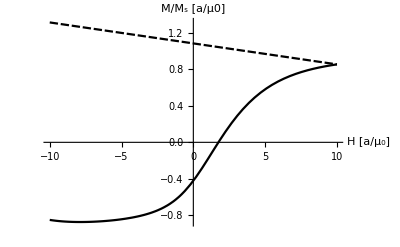

```mathematica
Plot[
{
Evaluate[M0[H]],
Evaluate[M1[H]]
},
{H,Hi0,Hf0},
PlotRange->{{Hi,Hf},All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
]
```

```mathematica
(M/.NDSolve[
{k M'[H]==L[(H+α M[H])/a]-M[H],M[Hi]==Mi},
M,{H,4,3}][[1,1]])
```

InterpolatingFunction[…]